# Fatter Skinnier Potential

## Potential

Pot: 1.0000000000000002 + x*(-8.881784197001252*^-16 + x*(-7.812499999999998 + x*(9.765625 + x*(10.68115234375 + x*(-37.384033203125 + x*(41.72325134277344 + x*(-25.331974029541016 + x*(8.96397978067398 + (-1.7462298274040222 + 0.14551915228366852*x)*x))))))))

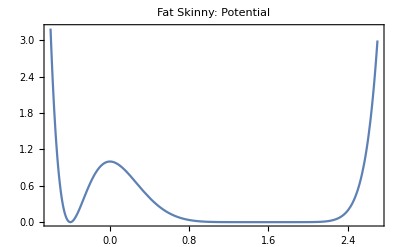

```mathematica
Pot=((8-5 x)^8 (2.+5 x)^2)/2^26;

Print["Pot: ",InputForm[HornerForm[Pot]]]

Plot[Pot,{x,-0.6,2.7},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Potential"]
```

## Force

Force: 0. + x*(15.625 + x*(-29.296875 + x*(-42.724609375 + x*(186.920166015625 + x*(-250.33950805664065 + x*(177.3238182067871 + x*(-71.71183824539185 + (15.716068446636202 - 1.4551915228366852*x)*x)))))))

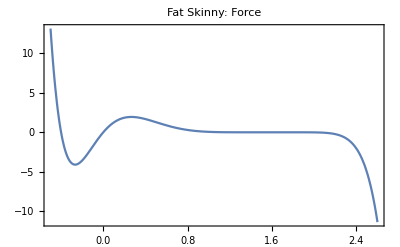

```mathematica
Force=-D[Pot,x];

Print["Force: ",InputForm[HornerForm[Force]]]

Plot[Force,{x,-0.5,2.6},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Force"]
```

## Hessian

Hessian: -15.625 + x*(58.59375 + x*(128.173828125 + x*(-747.6806640625 + x*(1251.6975402832031 + x*(-1063.9429092407227 + x*(501.9828677177429 + x*(-125.7285475730896 + 13.096723705530167*x)))))))

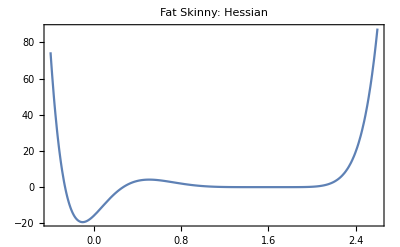

```mathematica
Hess=D[Pot,{x,2}];

Print["Hessian: ",InputForm[HornerForm[Hess]]]

Plot[Hess,{x,-0.4,2.6},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Hessian"]
```